# MathPRINSAS

## Basic Architecture of Program

Link to one note: http://tiny.cc/7wkvbz

## XLS Format

### Here is online converter from Access 97 MDB to XLS: https://www.mdbopener.com/

## GUI

## IMPORT/EXPORT DIALOGS

```mathematica
OpenDB[curDir_:$HomeDirectory]:=SystemDialogInput[
"FileOpen",
{
curDir,
{"excel 2000"->{"*.xls"},"mdb"->{"*.mdb"},"accdb"->{"*.accdb"}}
},
WindowTitle->"Import DataBase"];


SaveDB[fileName_,curDir_:$HomeDirectory] := SystemDialogInput[
"FileSave",
{
FileNameJoin[{curDir,fileName}],
{"excel 2000"->{"*.xls"}}
},
WindowTitle->"Export DataBase"];


getDBFromFile[filePath_]:=Module[
{
sheetsNames = Import[filePath,"Sheets"],
db=Import[filePath]
},
(*record file path and its name*)
Association@MapThread[ToString[#1]->#2&,{sheetsNames,db}]
];
```

## DATA RECONFIGURATION

```mathematica
sansRawDB=getDBFromFile[OpenDB[]]
```

<|DBInfo→{{Description},{SANS raw data - version 2}},DataMeasurements→{{File Number,Q,I(Q),Masked,dI(Q)},5621},DataFileInfo→{{File Number,Sample Number,Type of Measurement,Laboratory,Instrument,Thickness (mm),Wavelength (A),Transmission,Distance (m),File Name,Qmin,Qmax,Offset,Background,File Description,Sample Description},28,{N13483,Gordonstone 6m 1bar2 He,SANS,OR,SANS,2.00000000e+00,4.80000019e+00,0.00000000e+00,6.00000000e+00,N13483,8.75947438e-03,9.99999717e-02,0.00000000e+00,9.96182312e+02,ascii 2 column text,Gordonstone coarse powd. 2mm Al holder 1bar2 He}}|>
 |  |  |  |

### DataFileInfo parsing

```mathematica
(*TODO improve this function*)
parseDBToAssoc[db_]:=Module[
{
dataFileInfoTitles = Rest[First[db["DataFileInfo"]]],
dataMeasurmentTitles = Rest[First[db["DataMeasurements"]]],
fileNamesList = Rest[db["DataFileInfo"]][[All,1]],
dataFileInfoWithoutFirstRowAndColumn=db["DataFileInfo"][[2;;-1,2;;-1]],
dbinfoAssoc=Association@MapIndexed[#1->First@Flatten@Rest[db["DBInfo"]][[All,#2]]&,db["DBInfo"][[1]]],
getMeasurmentsAssoc,
filesAssoc,
FromMatrixStringExpressionToNumber
},

FromMatrixStringExpressionToNumber[matrixString_]:=Map[Read[StringToStream[#],Number]&,matrixString,{2}];
getMeasurmentsAssoc[fileName_]:=Association@MapIndexed[
dataMeasurmentTitles[[First[#2]]]->#1&,
FromMatrixStringExpressionToNumber@Transpose[Select[
db["DataMeasurements"],
First[#]===fileName&][[2;;-1,2;;-1]]
]
];
filesAssoc = 
Association@MapIndexed[
fileNamesList[[First[#2]]]->Association[{
"DataFileInfo"->Association@MapIndexed[(dataFileInfoTitles[[First[#2]]]->#1)&,#1],
"DataMeasurements"->getMeasurmentsAssoc[fileNamesList[[First[#2]]]]
}]&,
dataFileInfoWithoutFirstRowAndColumn
];
Association["files"->filesAssoc,"DBInfo"->dbinfoAssoc]
]
```

## FIT SANS AND USANS DEVELOPMENT

```mathematica
sansDB=parseDBToAssoc@getDBFromFile[OpenDB[]];
usansDB=parseDBToAssoc@getDBFromFile[OpenDB[]];
```

```mathematica
sansData=sansDB["files","N00001","DataMeasurements"];
usansData=usansDB["files","UN00001","DataMeasurements"];
sansData//Keys
usansData//Keys
sansData["Q"]
sansData["I(Q)"]
```

{Q,I(Q),Masked,dI(Q)}

{Theta (arc sec),Timer,Monitor,Masked,I(Q),dI(Q)}

{0.002567,0.002909,0.003251,0.003593,0.003936,0.004278,0.00462,0.004962,0.005304,0.005647,0.005989,0.006331,0.006673,0.007015,0.007358,0.0077,0.008042,0.008384,0.008726,0.009069,0.009411,0.009753,0.0101,0.01044,0.01078,0.01112,0.01146,0.01181,0.01215,0.01249,0.01283,0.01317,0.01352,0.01386,0.0142,0.01454,0.01489,0.01523,0.01557,0.01591,0.01625,0.0166,0.01694,0.01728,0.01762,0.01796,0.01831,0.01865,0.01899,0.01933,0.01968,0.02002,0.02036,0.0207,0.02104,0.02139,0.02173,0.02207,0.02241,0.02275,0.0231,0.02344,0.02378,0.02412,0.02446,0.02481,0.02515,0.02549,0.02583,0.02617,0.02652,0.02686,0.0272,0.02754,0.02788,0.02804,0.02823,0.02857,0.02891,0.02925,0.02959,0.02994,0.03028,0.03062,0.03096,0.0313,0.03164,0.03178,0.03199,0.03233,0.03267,0.03301,0.03335,0.0337,0.03404,0.03438,0.03472,0.03506,0.0354,0.03552,0.03575,0.03609,0.03643,0.03677,0.03711,0.03746,0.0378,0.03814,0.03848,0.03882,0.03916,0.03925,0.03951,0.03985,0.04019,0.04298,0.04672,0.05045,0.05418,0.0579,0.06163,0.06536,0.06908,0.0728,0.07652,0.08023,0.08395,0.08766,0.09137,0.09508,0.09878,0.1025,0.1062,0.1099,0.1136,0.1173,0.1209,0.1246,0.1283,0.132,0.1357,0.1393,0.143,0.1466,0.1503,0.154,0.1576,0.1612,0.1649,0.1685,0.1721,0.1758,0.1794,0.183,0.1866,0.1902,0.1938,0.1974,0.201,0.2046,0.2082,0.2117,0.2153,0.2189,0.2224,0.226,0.2295,0.2331,0.2366,0.2401,0.2436,0.2472,0.2507,0.2542,0.2577,0.2611,0.2646,0.2681,0.2716,0.275,0.2785,0.2819,0.2854,0.2888,0.2922,0.2956,0.299,0.3024,0.3058,0.3092,0.3126,0.316,0.3193,0.3227,0.326,0.3294,0.3327,0.336,0.3394,0.3427,0.346,0.3493,0.3525,0.3558,0.3591,0.3624,0.3656,0.3688,0.3721,0.3753,0.3785,0.3817,0.3849,0.3881,0.3913,0.3945,0.3977,0.4008,0.404,0.4071,0.4102,0.4134,0.4165,0.4196,0.4227,0.4258,0.4288,0.4319,0.435,0.438}

{1872.,1270.,913.9,689.3,537.6,433.3,366.8,304.2,258.7,224.1,198.9,167.6,153.1,135.2,127.8,113.9,100.8,93.8,86.01,80.22,75.04,70.84,63.69,59.34,55.06,51.81,49.08,45.47,42.97,40.57,40.01,37.14,35.15,35.09,32.09,31.33,30.31,28.91,27.22,27.85,25.84,24.69,23.94,22.76,20.96,22.18,20.22,20.46,20.16,19.,18.97,19.12,17.72,17.8,16.1,16.51,15.78,15.43,14.33,15.42,15.24,13.85,13.51,12.46,13.9,13.57,12.65,11.81,11.79,12.26,11.26,12.5,11.29,10.24,9.688,10.31,10.62,9.52,9.623,9.875,8.977,8.492,9.707,8.523,8.798,8.28,7.922,8.33,7.874,7.724,7.229,7.145,6.857,6.421,6.27,7.203,7.141,6.397,6.494,6.518,6.671,6.567,5.794,6.019,6.073,5.35,5.767,4.468,4.805,5.147,5.592,5.104,4.973,3.876,4.251,3.992,3.209,2.588,2.128,1.791,1.526,1.343,1.19,1.079,0.9797,0.9053,0.8602,0.8081,0.7831,0.745,0.7229,0.7045,0.6822,0.6756,0.6626,0.6471,0.6409,0.6313,0.628,0.6147,0.6156,0.6094,0.6003,0.5985,0.5946,0.5994,0.5975,0.5919,0.5874,0.5856,0.5757,0.5786,0.5732,0.5715,0.5697,0.5521,0.5454,0.5396,0.5262,0.5228,0.5216,0.5054,0.4865,0.4795,0.4684,0.4562,0.45,0.4314,0.4262,0.4108,0.3972,0.3879,0.3743,0.3601,0.3407,0.3267,0.3184,0.3022,0.2921,0.2738,0.265,0.2545,0.2389,0.2234,0.2131,0.2065,0.189,0.1791,0.1666,0.1521,0.1457,0.1332,0.125,0.1171,0.107,0.101,0.09963,0.08829,0.08526,0.08497,0.07779,0.07642,0.07121,0.06772,0.06476,0.06458,0.06391,0.06201,0.06116,0.05779,0.05971,0.05684,0.05564,0.05407,0.05521,0.05268,0.05186,0.05236,0.05007,0.05061,0.04671,0.05035,0.04478,0.04739,0.04754,0.04356,0.0458,0.04875,0.04257,0.04238}

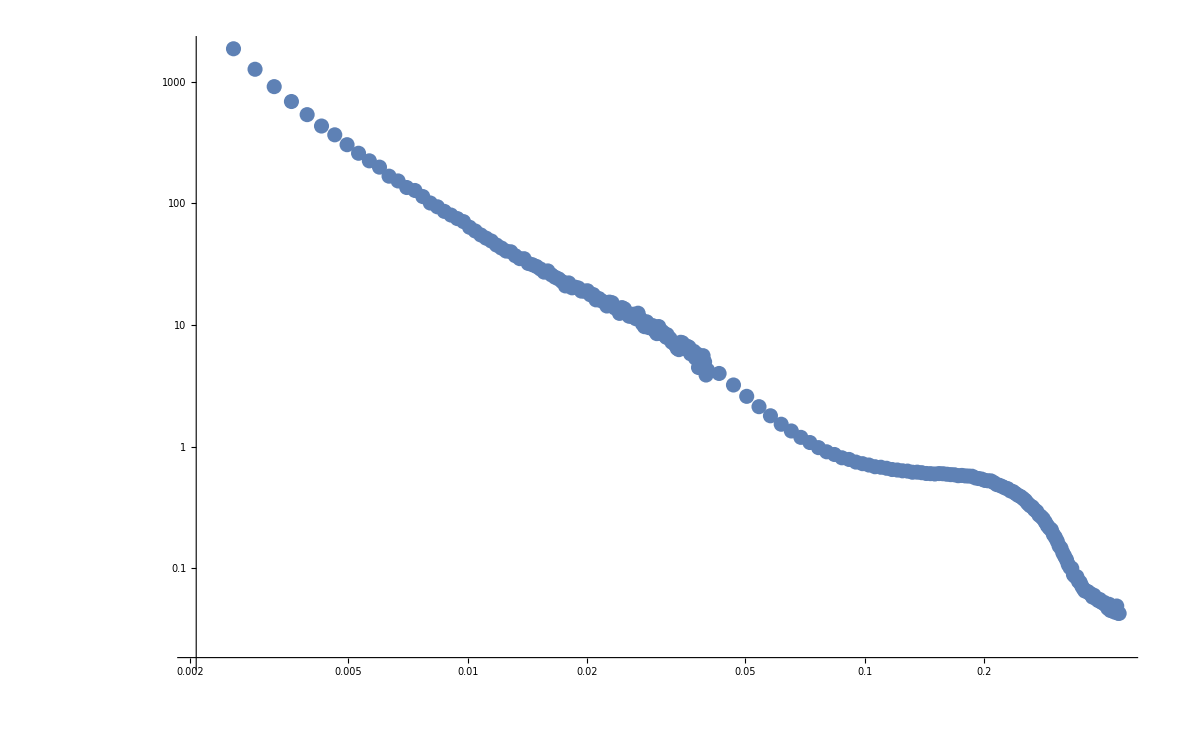

```mathematica
ListLogLogPlot[Transpose@{sansData["Q"],sansData["I(Q)"]}]
```

```mathematica
FitSANSandUSANS[sansData_,usansData_]:=Manipulate[ListLogLogPlot[Transpose@{sansData["Q"],sansData["I(Q)"]}],{a,1,10}]
```

## MAIN GUI INTERFACE

```mathematica
MainGUI[curDirrectory_]:=
CreateDialog[
Panel[
DynamicModule[
{
fileList={},
DBStructure=Association[],
selectedDB={},
selectedFile={},
selectedSANS,
selectedUSANS,
newFilename="newFileName",

(*Inner functionality*)
AddDB,

(*CallBacks and Windows*)
DisplayXLS,
OnImport,
OnEdit,
OnClear,
OnSaveAs,
OnRemoveItems,
OnCreateNew,
OnFitPressed
},


OnClear[]:=(
fileList={};
DBStructure=Association[];
selectedDB={});


AddDB[filePath_]:=Module[
{
fileName=FileBaseName[filePath],
dbAssoc=parseDBToAssoc[getDBFromFile[filePath]]
},
(*record file path and its name*)

DBStructure[fileName]=Association["path"->filePath];
DBStructure[fileName]["db"]=dbAssoc
];


OnImport[]:=Module[
{
importedFiles
},
importedFiles=OpenDB[curDirrectory];
If[Not[importedFiles===$Canceled],
If[ListQ[importedFiles],
AddDB/@importedFiles;
fileList=Union[fileList, FileBaseName/@importedFiles];
,
AddDB[importedFiles];
AppendTo[fileList,FileBaseName[importedFiles]];
];
selectedDB={First@fileList}
];
];


DisplayXLS[xlsAssoc_]:=CreateDialog[
TabView[
Flatten@KeyValueMap[
{#1->
TableView[#2,
Alignment->Center,
FieldSize->Medium,
ImageSize->{1300,600}
]}&,
DBStructure[xlsAssoc]["db"]],
ImageSize->{1330,650},
LabelStyle->{Bold}
]
];


OnEdit[selDB_]:=If[
Length[selDB]==1, 
DisplayXLS[First@selDB],
MessageDialog["Select only one DataBase: "<>ToString[selDB]]
];


OnSaveAs[selDB_]:=Module[
{
saveAsFilePath
},
If[
Length[selDB]==1, 
saveAsFilePath=SaveDB[First@selDB,curDirrectory];
If[Not[saveAsFilePath===$Canceled],
Export[saveAsFilePath,"Sheets"->Normal@DBStructure[First@selDB]["db"],"Rules"]
]
,
MessageDialog["Select only one DataBase: "<>ToString[selDB]]
]
];


OnRemoveItems[selDB_]:=
If[Length[selDB]≠0,
DBStructure=KeyDrop[DBStructure,selDB];
fileList=Complement[fileList,selDB];
selectedDB={},
MessageDialog["Select at least one database: "<>ToString[selDB]]
];


OnCreateNew[]:=
If[Not@MemberQ[fileList,newFilename],
AppendTo[fileList,newFilename];
DBStructure[newFilename]=Association["db"->Association[]],
MessageDialog["Such file name: "<>ToString[newFilename]<>", already exist"]
];

OnFitPressed[]:=Module[{},
If[KeyExistsQ[DBStructure,selectedSANS]&&KeyExistsQ[DBStructure,selectedUSANS],
CreateDialog[
FitSANSandUSANS[
DBStructure[selectedSANS],
DBStructure[selectedUSANS]
]
],
MessageDialog["selected SANS: '"<>ToString[selectedSANS]<>"' and USANS: '"<>ToString[selectedUSANS]<>"' are Invalid"]
]
];

Column[{
Grid[{
{
Text["File menu:"],
Button["Import File(s)",OnImport[],Background->LightBlue,Method->"Queued",ImageSize->{90,50}],
Column[{
Button["Create New",OnCreateNew[],Background->LightGreen,ImageSize->90],
InputField[Dynamic[newFilename],String,ContinuousAction->True,ImageSize->90]
}],
Button["Export File",OnSaveAs[selectedDB],Background->LightBlue,Method->"Queued",ImageSize->{90,50}],
Button["Detailed View",OnEdit[selectedDB],Background->LightGreen,ImageSize->{90,50}],
Button["Remove File(s)",OnRemoveItems[selectedDB],Background->LightRed,ImageSize->{90,50}],
Button["Clear All",OnClear[],Background->LightRed,ImageSize->{90,50}] 
},{},
{
Text["Fit SANS and USANS: "],
Button["Update SANS", selectedSANS={selectedDB, selectedFile},Background->LightBlue,ImageSize->{90,50}],
Dynamic@Text[" SANS: "<>ToString[Last[selectedSANS]]],
Button["Update USANS", selectedUSANS={selectedDB, selectedFile},Background->LightBlue,ImageSize->{90,50}],
Dynamic@Text[" USANS: "<>ToString[Last[selectedUSANS]]],
Button["Fit",OnFitPressed[],Background->LightYellow,Method->"Queued",ImageSize->90]
},{},
{
Text["Postprocessing"],Button["Postprocessing",Background->LightYellow,ImageSize->{90,50}]}
}],




Dynamic@If[
Length[fileList]>0,
Grid[{
{
Text["List of imported databases:"],
Text["Database description:"],
Text["List of Files:"],
Text["File details: "]
},

{
ListPicker[Dynamic[selectedDB],fileList,
Background->LightBlue,
FieldSize->{10,10},
Multiselection->False],

Text[DBStructure[First[selectedDB],"db","DBInfo","Description"]],

ListPicker[Dynamic[selectedFile],Keys@DBStructure[First[selectedDB],"db","files"],
Background->LightBlue,
FieldSize->{20,10},
Multiselection->False],

DBStructure[First[selectedDB],"db","files",First[selectedFile],"DataFileInfo"]
}
}
]],

Dynamic@If[Length[selectedDB]>=0,
Panel[
Grid[{selectedDB,Keys@DBStructure}]
],
Text[""]
]
}]
],
ImageSize->{720,700},
Background->White
],
WindowTitle->"MathPRINSAS"
];

MainGUI[NotebookDirectory[]]
```

qiau4_shm19FrontEndObject[LinkObject["qiau4_shm", 3, 1]]19MathPRINSAS

```mathematica
Dataset
```